```mathematica
(*importDir ="/home/gillen/Documents/Computation/saved_outputs/2D_Polar/Twist:0-180/Time_step:2.500000e-03__frames:50__Date:14-Oct-2015 13:01:42/";
nMatrix= Import[importDir<> "nMatrix.mat"]⟦1⟧;
avgEnergy = Import[importDir <> "avgEnergy.mat"]⟦1⟧;
*)

(* Sin[nMatrix⟦;;,;;,;;⟧]⟧*)
```

```mathematica
(*This is real janky, let me know if there's a better way to imbed data into a notebook*)
nMatrix = {{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117,0.0011524176214456117},{0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224,0.002304835242891224},{0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961,0.01533691902513961},{0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388,0.028369002807388},{0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407,0.1398531527651407},{0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936,0.2513373027228936},{0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844,0.8617869485132844},{1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753,1.4722365943036753},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457,0.012494229314833457},{0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924,0.024988458629666924},{0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302,0.08537395295967302},{0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916,0.14575944728967916},{0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428,0.3930672911208428},{0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072,0.6403751349520072},{1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289,1.333170183268289},{2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571,2.025965231584571},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754,0.036282618179556754},{0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355,0.07256523635911355},{0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423,0.18538662316747423},{0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513,0.29820800997583513},{0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554,0.6190444193236554},{0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764,0.9398808286714764},{1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154,1.6006801854775154},{2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555,2.261479542283555},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333,0.06999252916527333},{0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672,0.13998505833054672},{0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297,0.3005854008163297},{0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127,0.4611857433021127},{0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465,0.8186891667244465},{1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807,1.1761925901467807},{1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172,1.7873482928112172},{2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533,2.3985039954756533},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757,0.10489980265146757},{0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515,0.20979960530293515},{0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044,0.40648149823253044},{0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256,0.6031633911621256},{0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553,0.974961506654553},{1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802,1.3467596221469802},{1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977,1.914614270244977},{2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974,2.482468918342974},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308,0.13886322769386308},{0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261,0.2777264553877261},{0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993,0.5026344953619993},{0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721,0.7275425353362721},{1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152,1.1037763954640152},{1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574,1.4800102555917574},{2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683,2.011292086788683},{2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084,2.5425739179856084},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323,0.17144950737156323},{0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634,0.34289901474312634},{0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206,0.5910131695688206},{0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143,0.8391273243945143},{1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984,1.2150932043361984},{1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881,1.591059084277881},{2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834,2.0906023088005834},{2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852,2.5901455333232852},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803,0.19879365398629803},{0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959,0.3975873079725959},{0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611,0.6632469414943611},{0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256,0.9289065750161256},{1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632,1.3026288814990632},{1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992,1.6763511879819992},{2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854,2.1509588261339854},{2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971,2.625566464285971},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175,0.222454307610175},{0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986,0.44490861522034986},{0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347,0.7247701304764347},{1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184,1.0046316457325184},{1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027,1.3754547786886027},{1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858,1.7462779116446858},{2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955,2.200175133691955},{2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245,2.6540723557392245},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653,0.24359580381282653},{0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529,0.4871916076256529},{0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203,0.779193986992203},{1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753,1.071196366358753},{1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668,1.4389146830258668},{1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804,1.8066329996929804},{2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764,2.2425097497738764},{2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706,2.6783864998547706},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856,0.26058785489238856},{0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771,0.5211757097847771},{0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129,0.8226631946868129},{1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478,1.1241506795888478},{1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064,1.4891244096837064},{1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639,1.8540981397785639},{2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705,2.2757320383075705},{2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575,2.697365936836575},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513,0.27557196602511513},{0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302,0.5511439320502302},{0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345,0.8608480211893345},{1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438,1.170552110328438},{1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066,1.5329728553756066},{1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743,1.8953936004227743},{2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254,2.3045978370401254},{2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764,2.7138020736574764},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294,0.2875169082076294},{0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586,0.5750338164152586},{0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149,0.8912144773775149},{1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707,1.2073951383397707},{1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005,1.5677152464135005},{1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304,1.9280353544872304},{2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343,2.3273957026149343},{2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638,2.726756050742638},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793,0.2975410215923793},{0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584,0.5950820431847584},{0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968,0.9166603523876968},{1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635,1.238238661590635},{1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079,1.5967627520597079},{1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806,1.9552868425287806},{2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254,2.3464192238525254},{2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694,2.7375516051762694},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315,0.30632578110415315},{0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062,0.6126515622083062},{0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859,0.9389391493043859},{1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655,1.2652267364004655},{1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774,1.6221582980987774},{1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896,1.9790898597970896},{2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425,2.3630300513174425},{2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795,2.746970242837795},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924,0.31330154858793924},{0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784,0.6266030971758784},{0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871,0.9566197330829871},{1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955,1.2866363689900955},{1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095,1.642294105517095},{1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945,1.9979518420440945},{2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259,2.376190102903259},{2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236,2.7544283637624236},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689,0.319407339650689},{0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779,0.6388146793013779},{0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866,0.9720896183058866},{1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947,1.3053645573103947},{1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306,1.6599023296081306},{2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865,2.014440101905865},{2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173,2.3876925396297173},{2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677,2.7609449773535677},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016,0.32425206008162016},{0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401,0.6485041201632401},{0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682,0.9843615702339682},{1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957,1.3202190203046957},{1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711,1.6738656492323711},{2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454,2.0275122781600454},{2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663,2.3968111398755663},{2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844,2.7661100015910844},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543,0.32830619157267543},{0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506,0.6566123831453506},{0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258,0.9946294703083258},{1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002,1.3326465574713002},{1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646,1.6855461933548646},{2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428,2.038445829238428},{2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686,2.4044375528327686},{2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108,2.770429276427108},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554,0.3318526186376554},{0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108,0.6637052372753108},{1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772,1.0036106952500772},{1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434,1.3435161532248434},{1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536,1.695761628777536},{2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277,2.0480071043302277},{2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587,2.4111065612938587},{2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892,2.7742060182574892},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711,0.3346655324781711},{0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422,0.6693310649563422},{1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868,1.010733914000868},{1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393,1.352136763045393},{1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018,1.7038630231233018},{2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121,2.05558928320121},{2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538,2.416395041828538},{2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653,2.7772008004558653},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982,0.3371258913662982},{0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964,0.6742517827325964},{1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335,1.0169641284889335},{1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698,1.3596764742452698},{1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826,1.7109484012025826},{2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894,2.062220328159894},{2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324,2.4210200610290324},{2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684,2.7798197938981684},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581,0.3390772256761581},{0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316,0.678154451352316},{1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615,1.0219052619708615},{1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058,1.3656560725894058},{1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745,1.71656756720745},{2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932,2.0674790618254932},{2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699,2.424687892726699},{2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902,2.781896723627902},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125,0.3407096864113125},{0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248,0.6814193728226248},{1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941,1.026038893625941},{1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566,1.3706584144292566},{1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175,1.7212683268923175},{2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763,2.0718782393553763},{2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337,2.4277561916772337},{2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897,2.7836341439990897},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204,0.34213746253501204},{0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239,0.6842749250700239},{1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035,1.0296542021933035},{1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824,1.3750334793165824},{1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012,1.7253795955952012},{2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184,2.0757257118738184},{2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679,2.430439684256679},{2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539,2.785153656639539},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739,0.3432698050800739},{0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474,0.6865396101601474},{1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572,1.0325214201394572},{1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656,1.3785032301187656},{1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513,1.7286401207924513},{2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136,2.078777011466136},{2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426,2.4325678669089426},{2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747,2.786358722351747},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421,0.3442170873911421},{0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839,0.6884341747822839},{1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739,1.0349200368798739},{1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625,1.3814058989774625},{1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105,1.7313677510280105},{2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558,2.081329603078558},{2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568,2.4343482148334568},{2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354,2.787366826588354},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716,0.34504558397085716},{0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714,0.690091167941714},{1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803,1.0370178713734803},{1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457,1.3839445748052457},{1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785,1.7337533334817785},{2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831,2.08356209215831},{2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516,2.435905300707516},{2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215,2.7882485092567215},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806,0.3457026433316806},{0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608,0.6914052866633608},{1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203,1.0386816077939203},{1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783,1.3859579289244783},{1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534,1.7356452712059534},{2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426,2.085332613487426},{2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696,2.4371401790708696},{2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114,2.7889477446543114},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494,0.34627730825101494},{0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293,0.6925546165020293},{1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881,1.0401367124823881},{1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448,1.3877188084627448},{1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666,1.7372999587470666},{2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386,2.086881109031386},{2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495,2.4382202016926495},{2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116,2.7895592943539116},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577,0.34673305944013577},{0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709,0.6934661188802709},{1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153,1.0412907160087153},{1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567,1.3891153131371567},{1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969,1.738612244889969},{2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797,2.0881091766427797},{2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432,2.439076736646432},{2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082,2.790044296650082},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962,0.347114324155962},{0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235,0.6942286483119235},{1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389,1.0422561126898389},{1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529,1.3902835770677529},{1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461,1.7397100544161461},{2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537,2.089136531764537},{2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818,2.4397932814567818},{2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025,2.790450031149025},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087,0.34744777829309087},{0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813,0.6948955565861813},{1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361,1.0431004484953361},{1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902,1.3913053404044902},{1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671,1.740670198174671},{2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851,2.090035055944851},{2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778,2.4404199710781778},{2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042,2.7908048862115042},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405,0.3477122315174405},{0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807,0.6954244630348807},{1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717,1.0437700677094717},{1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615,1.3921156723840615},{1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902,1.7414316613000902},{2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186,2.0907476502161186},{2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464,2.4409169809792464},{2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763,2.7910863117423763},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905,0.3479435222568905},{0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809,0.6958870445137809},{1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216,1.0443557164990216},{1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633,1.3928243884842633},{1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807,1.7420976366683807},{2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992,2.0913708848524992},{2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088,2.441351665608088},{2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773,2.7913324463636773},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335,0.34812695249411335},{0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268,0.6962539049882268},{1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178,1.0448201782030178},{1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781,1.39338645141781},{1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757,1.7426258030983757},{2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433,2.0918651547789433},{2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604,2.4416964018008604},{2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785,2.7915276488227785},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302,0.3482804034024302},{0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605,0.6965608068048605},{1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125,1.045208729563125},{1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896,1.3938566523213896},{1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331,1.743067647438331},{2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274,2.092278642555274},{2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499,2.441984795232499},{2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725,2.791690947909725},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426,0.34841461152012426},{0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486,0.6968292230402486},{1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386,1.0455485564576386},{1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029,1.394267889875029},{1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134,1.743454084344134},{2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394,2.0926402788132394},{2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607,2.442237024020607},{2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764,2.7918337692279764},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643,0.3485210482279643},{0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287,0.6970420964559287},{1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168,1.0458180636682168},{1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045,1.3945940308805045},{1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827,1.7437605566458827},{2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262,2.092927082411262},{2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164,2.4424370596145164},{2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772,2.791947036817772},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303,0.3486141377378303},{0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606,0.6972282754756606},{1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462,1.04605377458462},{1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798,1.3948792736935798},{1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083,1.7440285972155083},{2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386,2.0931779207374386},{2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276,2.442612010674276},{2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115,2.792046100611115},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806,0.34868796442561806},{0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362,0.6973759288512362},{1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782,1.046240710321782},{1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328,1.395105491792328},{1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973,1.7442411726950973},{2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676,2.0933768535978676},{2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077,2.442750759466077},{2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288,2.792124665334288},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085,0.34874972508076085},{0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522,0.697499450161522},{1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072,1.046397093791072},{1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235,1.3952947374206235},{1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196,1.7444190054163196},{2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156,2.0935432734120156},{2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564,2.4428668315321564},{2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973,2.7921903896522973},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768,0.3488037409288768},{0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754,0.697607481857754},{1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203,1.046533866720203},{1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537,1.3954602515826537},{1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345,1.74457453785345},{2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477,2.0936888241242477},{2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715,2.4429683481211715},{2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948,2.7922478721180948},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703,0.3488465793875703},{0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412,0.6976931587751412},{1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804,1.0466423375055804},{1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213,1.3955915162360213},{1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048,1.7446978862798048},{2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904,2.0938042563235904},{2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832,2.443048858088832},{2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075,2.792293459854075},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559,0.3488824164451559},{0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121,0.6977648328903121},{1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223,1.0467330801209223},{1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533,1.395701327351533},{1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457,1.7448010749748457},{2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603,2.0939008225981603},{2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873,2.4431162097262873},{2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165,2.7923315968544165},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128,0.3489137595235128},{0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257,0.6978275190470257},{1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524,1.0468124435813524},{1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792,1.3957973681156792},{1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714,1.7448913237722714},{2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645,2.0939852794288645},{2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356,2.443175115445356},{2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185,2.79236495146185},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619,0.3489386168424619},{0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924,0.697877233684924},{1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361,1.0468753845224361},{1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485,1.3958735353599485},{1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876,1.7449628975696876},{2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278,2.0940522597794278},{2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235,2.4432218319238235},{2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822,2.79239140406822},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343,0.3489603570451343},{0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687,0.6979207140902687},{1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244,1.0469304326480244},{1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578,1.39594015120578},{1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597,1.7450254959884597},{2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141,2.094110840771141},{2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233,2.4432626901399233},{2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066,2.7924145395087066},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174,0.34897759859191174},{0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236,0.6979551971838236},{1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095,1.0469740897770095},{1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195,1.395992982370195},{1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166,1.7450751410438166},{2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439,2.094157299717439},{2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027,2.4432950936485027},{2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567,2.792432887579567},{3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793,3.141592653589793}}};
```

```mathematica
avgEnergy = {{1.4989461684154475,0.5595805965232183,0.3466701536776952,0.26932056654907227,0.22630126377254356,0.20126045129547585,0.18474095301012639,0.17307551274069083,0.16550766138379694,0.1602631665253489,0.15646301505923263,0.1539607247702536,0.15213798017890476,0.1509327200405888,0.15008658891435236,0.14946702857205113,0.14905528914978364,0.14875274931203492,0.14855092579414075,0.14840794576235833,0.14830218373534693,0.14823109237720844,0.1481781812030653,0.14814236289594368,0.14811657225935787,0.14809713182034406,0.14808378107282605,0.14807401668320816,0.14806652541067472,0.14806127996817653,0.14805719674730328,0.14805429311629198,0.1480520914535065,0.1480503357050018,0.14804905593876205,0.1480480183570342,0.14804724968449476,0.14804664347586136,0.14804614079396092,0.14804576038119296,0.14804544090653962,0.14804519632040672,0.14804499767536203,0.14804482839638466,0.14804469710225232,0.14804458927541103,0.14804449647038612,0.1480444238646917,0.14804436108558108,0.14804431177610866}};
```

```mathematica
(*Manipulate[ListVectorPlot[XYMatrix⟦frame,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All],{frame,1,frames,1}]*)
```

```mathematica
(*Manipulate[ListDensityPlot[Sin[θMatrix⟦frame⟧]^2 ᵀ,ColorFunctionScaling->False,ColorFunction->GrayLevel],{frame,1,frames,1}]*)
```

```mathematica
Dimensions@nMatrix;
(*nMatrix=Transpose[nMatrix,{1,4,2,3}];*)
{frames,ϕ}=Dimensions[nMatrix]⟦;;-2⟧
(*θMatrix=ArcTan[nMatrix⟦;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,2⟧];*)
θMatrix=nMatrix⟦;;,;;,;;⟧;
XYMatrix= Through[{Cos, Sin}[nMatrix]];
XYMatrix = Transpose[XYMatrix, {4,1,2,3}];
Dimensions@XYMatrix
```

{50,10}

{50,10,10,2}

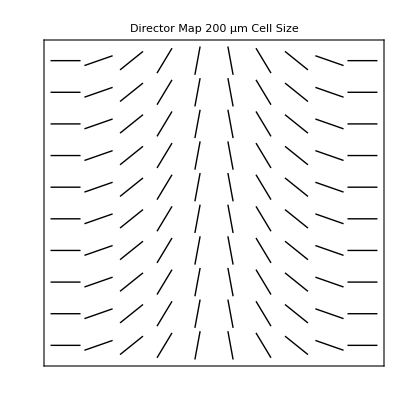

```mathematica
ListVectorPlot[XYMatrix⟦50,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All,PlotLabel->"Director Map 200 μm Cell Size", PlotTheme->"Monochrome",FrameTicks->None]
```

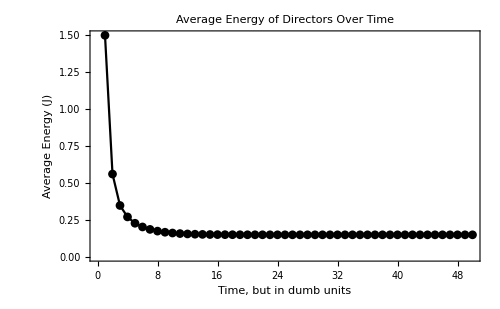

```mathematica
ListPlot[avgEnergy, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

```mathematica
t = Range[0,(2.5*^-3)*49,2.5*^-3]
```

{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225}

```mathematica
Energy = avgEnergy[[1,;;]];
```

```mathematica
data=Thread[t,Energy];
Dimensions[Energy]
Dimensions[t]
```

{50}

{50}

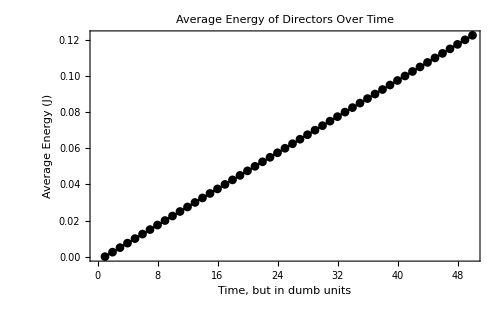

```mathematica
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

```mathematica
data=Thread[Energy,t];
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

-Graphics-

```mathematica
(*To fix the x-axis, use paired data like so*)
```

```mathematica
data//Length
```

50

```mathematica
(*Change the 0.05 to whatever your time step is*)
timedata=Range[0,49]*0.05
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45}

```mathematica
(*This puts the lists one after another*)
{timedata,data}
```

{{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45},{1.49895,0.559581,0.34667,0.269321,0.226301,0.20126,0.184741,0.173076,0.165508,0.160263,0.156463,0.153961,0.152138,0.150933,0.150087,0.149467,0.149055,0.148753,0.148551,0.148408,0.148302,0.148231,0.148178,0.148142,0.148117,0.148097,0.148084,0.148074,0.148067,0.148061,0.148057,0.148054,0.148052,0.14805,0.148049,0.148048,0.148047,0.148047,0.148046,0.148046,0.148045,0.148045,0.148045,0.148045,0.148045,0.148045,0.148044,0.148044,0.148044,0.148044}}

```mathematica
(*And this matches them up pairwise. The little ᵀ is a Transpose[] function that can be entered with "esc tr esc"*)
```

```mathematica
paireddata={timedata,data}ᵀ
```

{{0.,1.49895},{0.05,0.559581},{0.1,0.34667},{0.15,0.269321},{0.2,0.226301},{0.25,0.20126},{0.3,0.184741},{0.35,0.173076},{0.4,0.165508},{0.45,0.160263},{0.5,0.156463},{0.55,0.153961},{0.6,0.152138},{0.65,0.150933},{0.7,0.150087},{0.75,0.149467},{0.8,0.149055},{0.85,0.148753},{0.9,0.148551},{0.95,0.148408},{1.,0.148302},{1.05,0.148231},{1.1,0.148178},{1.15,0.148142},{1.2,0.148117},{1.25,0.148097},{1.3,0.148084},{1.35,0.148074},{1.4,0.148067},{1.45,0.148061},{1.5,0.148057},{1.55,0.148054},{1.6,0.148052},{1.65,0.14805},{1.7,0.148049},{1.75,0.148048},{1.8,0.148047},{1.85,0.148047},{1.9,0.148046},{1.95,0.148046},{2.,0.148045},{2.05,0.148045},{2.1,0.148045},{2.15,0.148045},{2.2,0.148045},{2.25,0.148045},{2.3,0.148044},{2.35,0.148044},{2.4,0.148044},{2.45,0.148044}}

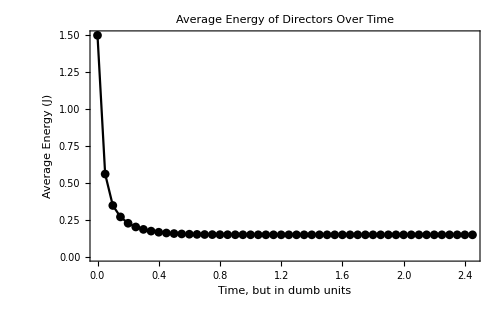

```mathematica
ListPlot[paireddata, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```